```mathematica
Germination Model 
Revision 9-6-2021
```

0≤f≤1, 0≤g≤1, 0≤g+γ≤1, all other parameters must be positive.
Plants are obligate when rP=bP*f*g-dP ≤ 0 or facultative otherwise.
Animals are obligate when rA=bA-dA ≤ 0 or facultative otherwise.

Obligate Plants, Obligate Animals

{-4.,0}

{0,-3.33333}

{{P→2.13781,A→5.26706},{P→0.708168,A→1.67677}}

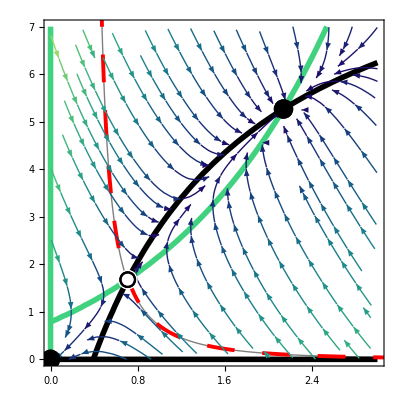

```mathematica
(* Obligate Plants, Obligate Animals *) 
Print["Obligate Plants, Obligate Animals" ]

bP=1; f = 1; g=0.5;γ =0.5;sP=0.05; dP=0.7; 
a=0.85;h=1;
bA=1; ε=2; sA=0.15; dA=1.5;
maxP=3;maxA=7;

plantColor =RGBColor[65/256,211/256,129/256];
animalColor = Black;
pointSize = 0.035;
imageSize=15;
lineThickness = 0.01;

(*Non-trivial nullcline equations for model. Using these to plot avoids numerical plotting issues.*)
nP[P_,A_]=bP*f*(g+γ*(a*A)/(1+a*h*P+a*A))-sP*P-dP; 
nA[P_,A_]=bA+ε*(a*P)/(1+a*h*P)-sA*A - dA;
(* Vector Plot *)
(*vp=Evaluate[VectorPlot[{nP[P,A],nA[P,A]},{P,minP,maxP},{A,minA,maxA},Axes->True,AxesLabel->{"P","A"},VectorPoints->8,VectorStyle->{Thick},VectorScale-> {0.08,0.8,None},VectorColorFunction->"BlueGreenYellow"]];*)

(* Stream Plot *) 
sp=Evaluate[StreamPlot[{nP[P,A],nA[P,A]},{P,minP,maxP},{A,minA,maxA},Axes->True,StreamColorFunction->"BlueGreenYellow", StreamScale->Large]];

(* Non-Trivial Nullclines *)
cpP=ContourPlot[{nP[P,A]==0},{P,minP,maxP},{A,minA,maxA}, ColorFunction->Function[{x},plantColor],ContourStyle->{Thickness[lineThickness]}];
cpA=ContourPlot[{nA[P,A]==0},{P,minP,maxP},{A,minA,maxA}, ColorFunction->Function[{x},animalColor],ContourStyle->{Thickness[lineThickness]}];

(* Trivial Nullclines *)
zeroP=Line[{{0,minA},{0,maxA}}]; 
trivialP=Graphics[{Thickness[lineThickness],plantColor,zeroP}];
zeroA=Line[{{minP,0},{maxP,0}}]; 
trivialA=Graphics[{Thickness[lineThickness],animalColor,zeroA}];

(* Asymptotes [Saturation Points] *)
saturA = ε/(h*sA)+(bA-dA)/(sA);
asympA = Line[{{minA,saturA},{maxA,saturA}}];
asympA=Graphics[{Thickness[lineThickness],Dashing[{0.03,0.05,0.03}],animalColor,asympA}];

(* Trivial & Single-Species Equilibria *) 
plantonlyeq = {(bP*f*g-dP)/sP,0} 
preplantonlypt = ListPlot[{plantonlyeq}, PlotStyle->{Red, PointSize[pointSize]}];
plantonlypt=ListPlot[{plantonlyeq},PlotMarkers->Graphics[{Black,Circle[]},ImageSize->imageSize]];
 
animalonlyeq={0,(bA-dA)/sA}
preanimalonlypt=ListPlot[{animalonlyeq},PlotStyle->{Red, PointSize[pointSize]}];
animalonlypt=ListPlot[{animalonlyeq},PlotMarkers->Graphics[{Black, Circle[]},ImageSize->imageSize]];

trivialeq={0,0};
pretrivialpt=ListPlot[{trivialeq},PlotStyle->{Black,PointSize[pointSize]}]; 
trivialpt=ListPlot[{trivialeq},PlotMarkers->Graphics[{Black,Circle[]},ImageSize->imageSize]];

(* Coexistence Equilibria *) 
(*Finds the equilibria for the model. I manually assigned names for unstable and stable equilbiria.*)
equilibria= NSolve[nP[P,A]==0&&nA[P,A]==0&&P>0&&A>0,{P,A}];
equilibria

coexist1={P/.equilibria[[1]],A/.equilibria[[1]]};
precoexistpt1=ListPlot[{coexist1},PlotStyle->{Black, PointSize[0.035]}];
coexistpt1=ListPlot[{coexist1},PlotMarkers->Graphics[{Black,Circle[]},ImageSize->imageSize]];

coexist2={P/.equilibria[[2]],A/.equilibria[[2]]}; 
precoexistpt2=ListPlot[{coexist2},PlotStyle->{White, PointSize[0.035]}];
coexistpt2=ListPlot[{coexist2},PlotMarkers->Graphics[{Black,Circle[]},ImageSize->imageSize]];

(* Separatrices *) 
(*Finds the separatrices numerically. Using the full model avoids numerical plotting issues. Sep1 and Sep2 comprise the stable manifold while Sep3 and Sep4 comprise the unstable manifold.*)
FP[P_,A_]=P*(bP*f*(g+γ*(a*A)/(1+a*h*P+a*A))-sP*P-dP); 
FA[P_,A_]=A*(bA+ε*(a*P)/(1+a*h*P)-sA*A - dA);
eps=1/100;sol[{P0_,A0_,tmin_,tmax_}]:=NDSolveValue[{P'[t]==FP[P[t],A[t]],A'[t]==FA[P[t],A[t]],P[0]==P0,A[0]==A0},{P[t],A[t]},{t,tmin,tmax}]

sepxylim=17;sepyxlim=10;
sepformat ={Red,Thickness[0.007],Dashing[{0.05,0.05}]};
sepxy2=ParametricPlot[Evaluate@sol[{coexist2[[1]]+eps,coexist2[[2]]-eps,-sepxylim,0}],{t,-sepxylim,0},PlotStyle->sepformat];
sepyx2=ParametricPlot[Evaluate@sol[{coexist2[[1]]-eps,coexist2[[2]]+eps,-sepyxlim,0}],{t,-sepyxlim,0},PlotStyle->sepformat];

(* for shading *) 
sepformat ={Gray,Thin};
sepformxy=ParametricPlot[Evaluate@sol[{coexist2[[1]]+eps,coexist2[[2]]-eps,-sepxylim,0}],{t,-sepxylim,0},PlotStyle->sepformat];
sepyformyx=ParametricPlot[Evaluate@sol[{coexist2[[1]]-eps,coexist2[[2]]+eps,-sepyxlim,0}],{t,-sepyxlim,0},PlotStyle->sepformat];

Show[cpP, cpA,sepformxy,sepyformyx, trivialP,trivialA, sepxy2,sepyx2, sp,pretrivialpt,trivialpt, preanimalonlypt,animalonlypt,preplantonlypt,plantonlypt, precoexistpt1, coexistpt1, precoexistpt2,coexistpt2,PlotRangePadding->{{maxP*0.025,0},{maxA*0.025,0}}]
```

Obligate Plants, Facultative Animals

{-4.,0}

{0,0.5}

{{P→1.14242,A→2.72175},{P→0.246911,A→1.23684}}

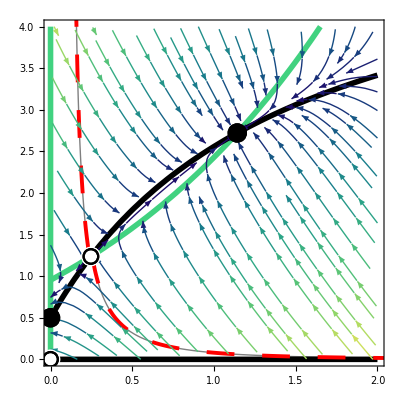

```mathematica
(* Obligate Plants, Facultative Animals *) 
Print["Obligate Plants, Facultative Animals" ]

bP=1; f = 1; g=0.5;γ =0.5;sP=0.05; dP=0.7; 
a=0.7;h=1;
bA=1; ε=1; sA=0.2; dA=0.9;
maxP=2;maxA=4;

plantColor =RGBColor[65/256,211/256,129/256];
animalColor = Black;
pointSize = 0.035;
imageSize=15;
lineThickness = 0.01;

(*Non-trivial nullcline equations for model. Using these to plot avoids numerical plotting issues.*)
nP[P_,A_]=bP*f*(g+γ*(a*A)/(1+a*h*P+a*A))-sP*P-dP; 
nA[P_,A_]=bA+ε*(a*P)/(1+a*h*P)-sA*A - dA;
(* Vector Plot *)
(*vp=Evaluate[VectorPlot[{nP[P,A],nA[P,A]},{P,minP,maxP},{A,minA,maxA},Axes->True,AxesLabel->{"P","A"},VectorPoints->8,VectorStyle->{Thick},VectorScale-> {0.08,0.8,None},VectorColorFunction->"BlueGreenYellow"]];*)

(* Stream Plot *) 
sp=Evaluate[StreamPlot[{nP[P,A],nA[P,A]},{P,minP,maxP},{A,minA,maxA},Axes->True,StreamColorFunction->"BlueGreenYellow", StreamScale->Large]];

(* Non-Trivial Nullclines *)
cpP=ContourPlot[{nP[P,A]==0},{P,minP,maxP},{A,minA,maxA}, ColorFunction->Function[{x},plantColor],ContourStyle->{Thickness[lineThickness]}];
cpA=ContourPlot[{nA[P,A]==0},{P,minP,maxP},{A,minA,maxA}, ColorFunction->Function[{x},animalColor],ContourStyle->{Thickness[lineThickness]}];

(* Trivial Nullclines *)
zeroP=Line[{{0,minA},{0,maxA}}]; 
trivialP=Graphics[{Thickness[lineThickness],plantColor,zeroP}];
zeroA=Line[{{minP,0},{maxP,0}}]; 
trivialA=Graphics[{Thickness[lineThickness],animalColor,zeroA}];

(* Asymptotes [Saturation Points] *)
saturA = ε/(h*sA)+(bA-dA)/(sA);
asympA = Line[{{minA,saturA},{maxA,saturA}}];
asympA=Graphics[{Thickness[lineThickness],Dashing[{0.03,0.05,0.03}],animalColor,asympA}];

(* Trivial & Single-Species Equilibria *) 
plantonlyeq = {(bP*f*g-dP)/sP,0} 
preplantonlypt = ListPlot[{plantonlyeq}, PlotStyle->{Black, PointSize[pointSize]}];
plantonlypt=ListPlot[{plantonlyeq},PlotMarkers->Graphics[{Black,Circle[]},ImageSize->imageSize]];
 
animalonlyeq={0,(bA-dA)/sA}
preanimalonlypt=ListPlot[{animalonlyeq},PlotStyle->{Black, PointSize[pointSize]}];
animalonlypt=ListPlot[{animalonlyeq},PlotMarkers->Graphics[{Black, Circle[]},ImageSize->imageSize]];

trivialeq={0,0};
pretrivialpt=ListPlot[{trivialeq},PlotStyle->{White,PointSize[pointSize]}]; 
trivialpt=ListPlot[{trivialeq},PlotMarkers->Graphics[{Black,Circle[]},ImageSize->imageSize]];

(* Coexistence Equilibria *) 
(*Finds the equilibria for the model. I manually assigned names for unstable and stable equilbiria.*)
equilibria= NSolve[nP[P,A]==0&&nA[P,A]==0&&P>0&&A>0,{P,A}];
equilibria

coexist1={P/.equilibria[[1]],A/.equilibria[[1]]};
precoexistpt1=ListPlot[{coexist1},PlotStyle->{Black, PointSize[0.035]}];
coexistpt1=ListPlot[{coexist1},PlotMarkers->Graphics[{Black,Circle[]},ImageSize->imageSize]];

coexist2={P/.equilibria[[2]],A/.equilibria[[2]]}; 
precoexistpt2=ListPlot[{coexist2},PlotStyle->{White, PointSize[0.035]}];
coexistpt2=ListPlot[{coexist2},PlotMarkers->Graphics[{Black,Circle[]},ImageSize->imageSize]];

(* Separatrices *) 
(*Finds the separatrices numerically. Using the full model avoids numerical plotting issues. Sep1 and Sep2 comprise the stable manifold while Sep3 and Sep4 comprise the unstable manifold.*)
FP[P_,A_]=P*(bP*f*(g+γ*(a*A)/(1+a*h*P+a*A))-sP*P-dP); 
FA[P_,A_]=A*(bA+ε*(a*P)/(1+a*h*P)-sA*A - dA);
eps=1/100;sol[{P0_,A0_,tmin_,tmax_}]:=NDSolveValue[{P'[t]==FP[P[t],A[t]],A'[t]==FA[P[t],A[t]],P[0]==P0,A[0]==A0},{P[t],A[t]},{t,tmin,tmax}]

sepxylim=25;sepyxlim=13;
sepformat ={Red,Thickness[0.007],Dashing[{0.05,0.05}]};
sepxy2=ParametricPlot[Evaluate@sol[{coexist2[[1]]+eps,coexist2[[2]]-eps,-sepxylim,0}],{t,-sepxylim,0},PlotStyle->sepformat];
sepyx2=ParametricPlot[Evaluate@sol[{coexist2[[1]]-eps,coexist2[[2]]+eps,-sepyxlim,0}],{t,-sepyxlim,0},PlotStyle->sepformat];

(* for shading *) 
sepformat ={Gray,Thin};
sepformxy=ParametricPlot[Evaluate@sol[{coexist2[[1]]+eps,coexist2[[2]]-eps,-sepxylim,0}],{t,-sepxylim,0},PlotStyle->sepformat];
sepyformyx=ParametricPlot[Evaluate@sol[{coexist2[[1]]-eps,coexist2[[2]]+eps,-sepyxlim,0}],{t,-sepyxlim,0},PlotStyle->sepformat];

Show[cpP, cpA,sepformxy,sepyformyx,trivialP,trivialA, sepxy2,sepyx2, sp,pretrivialpt,trivialpt, preanimalonlypt,animalonlypt,preplantonlypt,plantonlypt, precoexistpt1, coexistpt1, precoexistpt2,coexistpt2,PlotRangePadding->{{maxP*0.025,0},{maxA*0.025,0}}]
```

Obligate Plants, Facultative Animals

{-4.,0}

{0,2.}

{{P→2.12494,A→5.21823}}

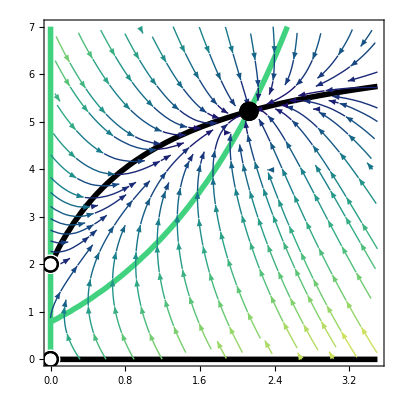

```mathematica
(* Obligate Plants, Facultative Animals *) 
Print["Obligate Plants, Facultative Animals" ]

bP=1; f = 1; g=0.5;γ =0.5;sP=0.05; dP=0.7; 
a=0.85;h=1;
bA=1; ε=1; sA=0.2; dA=0.6;
maxP=3.5;maxA=7;

plantColor =RGBColor[65/256,211/256,129/256];
animalColor = Black;
pointSize = 0.035;
imageSize=15;
lineThickness = 0.01;

(*Non-trivial nullcline equations for model. Using these to plot avoids numerical plotting issues.*)
nP[P_,A_]=bP*f*(g+γ*(a*A)/(1+a*h*P+a*A))-sP*P-dP; 
nA[P_,A_]=bA+ε*(a*P)/(1+a*h*P)-sA*A - dA;
(* Vector Plot *)
(*vp=Evaluate[VectorPlot[{nP[P,A],nA[P,A]},{P,minP,maxP},{A,minA,maxA},Axes->True,AxesLabel->{"P","A"},VectorPoints->8,VectorStyle->{Thick},VectorScale-> {0.08,0.8,None},VectorColorFunction->"BlueGreenYellow"]];*)

(* Stream Plot *) 
sp=Evaluate[StreamPlot[{nP[P,A],nA[P,A]},{P,minP,maxP},{A,minA,maxA},Axes->True,StreamColorFunction->"BlueGreenYellow", StreamScale->Large]];

(* Non-Trivial Nullclines *)
cpP=ContourPlot[{nP[P,A]==0},{P,minP,maxP},{A,minA,maxA}, ColorFunction->Function[{x},plantColor],ContourStyle->{Thickness[lineThickness]}];
cpA=ContourPlot[{nA[P,A]==0},{P,minP,maxP},{A,minA,maxA}, ColorFunction->Function[{x},animalColor],ContourStyle->{Thickness[lineThickness]}];

(* Trivial Nullclines *)
zeroP=Line[{{0,minA},{0,maxA}}]; 
trivialP=Graphics[{Thickness[lineThickness],plantColor,zeroP}];
zeroA=Line[{{minP,0},{maxP,0}}]; 
trivialA=Graphics[{Thickness[lineThickness],animalColor,zeroA}];

(* Asymptotes [Saturation Points] *)
saturA = ε/(h*sA)+(bA-dA)/(sA);
asympA = Line[{{minA,saturA},{maxA,saturA}}];
asympA=Graphics[{Thickness[lineThickness],Dashing[{0.03,0.05,0.03}],animalColor,asympA}];

(* Trivial & Single-Species Equilibria *) 
plantonlyeq = {(bP*f*g-dP)/sP,0} 
preplantonlypt = ListPlot[{plantonlyeq}, PlotStyle->{Red, PointSize[pointSize]}];
plantonlypt=ListPlot[{plantonlyeq},PlotMarkers->Graphics[{Black,Circle[]},ImageSize->imageSize]];
 
animalonlyeq={0,(bA-dA)/sA}
preanimalonlypt=ListPlot[{animalonlyeq},PlotStyle->{White, PointSize[pointSize]}];
animalonlypt=ListPlot[{animalonlyeq},PlotMarkers->Graphics[{Black, Circle[]},ImageSize->imageSize]];

trivialeq={0,0};
pretrivialpt=ListPlot[{trivialeq},PlotStyle->{White,PointSize[pointSize]}]; 
trivialpt=ListPlot[{trivialeq},PlotMarkers->Graphics[{Black,Circle[]},ImageSize->imageSize]];

(* Coexistence Equilibria *) 
(*Finds the equilibria for the model. I manually assigned names for unstable and stable equilbiria.*)
equilibria= NSolve[nP[P,A]==0&&nA[P,A]==0&&P>0&&A>0,{P,A}];
equilibria

coexist1={P/.equilibria[[1]],A/.equilibria[[1]]};
precoexistpt1=ListPlot[{coexist1},PlotStyle->{Black, PointSize[0.035]}];
coexistpt1=ListPlot[{coexist1},PlotMarkers->Graphics[{Black,Circle[]},ImageSize->imageSize]];

Show[cpP, cpA,trivialP,trivialA, sp,pretrivialpt,trivialpt, preanimalonlypt,animalonlypt,preplantonlypt,plantonlypt, precoexistpt1, coexistpt1,PlotRangePadding->{{maxP*0.025,0},{maxA*0.025,0}}]
```

Facultative Plants, Obligate Animals

{0.4,0}

{0,-2.5}

{{P→2.77447,A→1.17531},{P→1.14987,A→0.174283}}

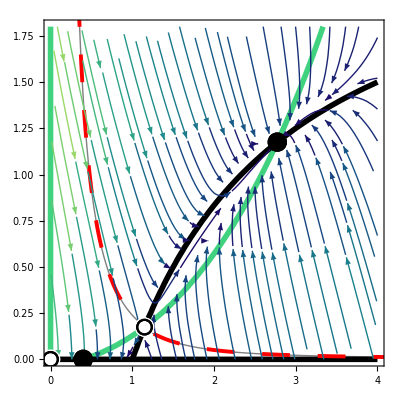

```mathematica
(* Facultative Plants, Obligate Animals *) 
Print["Facultative Plants, Obligate Animals" ]

bP=1; f = 1; g=0.5;γ =0.5;sP=0.05; dP=0.48; 
a=1;h=1;
bA=1; ε=1; sA=0.2; dA=1.5;
maxP=4;maxA=1.8;

plantColor =RGBColor[65/256,211/256,129/256];
animalColor = Black;
pointSize = 0.035;
imageSize=15;
lineThickness = 0.01;

(*Non-trivial nullcline equations for model. Using these to plot avoids numerical plotting issues.*)
nP[P_,A_]=bP*f*(g+γ*(a*A)/(1+a*h*P+a*A))-sP*P-dP; 
nA[P_,A_]=bA+ε*(a*P)/(1+a*h*P)-sA*A - dA;
(* Vector Plot *)
(*vp=Evaluate[VectorPlot[{nP[P,A],nA[P,A]},{P,minP,maxP},{A,minA,maxA},Axes->True,AxesLabel->{"P","A"},VectorPoints->8,VectorStyle->{Thick},VectorScale-> {0.08,0.8,None},VectorColorFunction->"BlueGreenYellow"]];*)

(* Stream Plot *) 
sp=Evaluate[StreamPlot[{nP[P,A],nA[P,A]},{P,minP,maxP},{A,minA,maxA},Axes->True,StreamColorFunction->"BlueGreenYellow", StreamScale->Large]];

(* Non-Trivial Nullclines *)
cpP=ContourPlot[{nP[P,A]==0},{P,minP,maxP},{A,minA,maxA}, ColorFunction->Function[{x},plantColor],ContourStyle->{Thickness[lineThickness]}];
cpA=ContourPlot[{nA[P,A]==0},{P,minP,maxP},{A,minA,maxA}, ColorFunction->Function[{x},animalColor],ContourStyle->{Thickness[lineThickness]}];

(* Trivial Nullclines *)
zeroP=Line[{{0,minA},{0,maxA}}]; 
trivialP=Graphics[{Thickness[lineThickness],plantColor,zeroP}];
zeroA=Line[{{minP,0},{maxP,0}}]; 
trivialA=Graphics[{Thickness[lineThickness],animalColor,zeroA}];

(* Asymptotes [Saturation Points] *)
saturA = ε/(h*sA)+(bA-dA)/(sA);
asympA = Line[{{minA,saturA},{maxA,saturA}}];
asympA=Graphics[{Thickness[lineThickness],Dashing[{0.03,0.05,0.03}],animalColor,asympA}];

(* Trivial & Single-Species Equilibria *) 
plantonlyeq = {(bP*f*g-dP)/sP,0} 
preplantonlypt = ListPlot[{plantonlyeq}, PlotStyle->{Black, PointSize[pointSize]}];
plantonlypt=ListPlot[{plantonlyeq},PlotMarkers->Graphics[{Black,Circle[]},ImageSize->imageSize]];
 
animalonlyeq={0,(bA-dA)/sA}
preanimalonlypt=ListPlot[{animalonlyeq},PlotStyle->{Red, PointSize[pointSize]}];
animalonlypt=ListPlot[{animalonlyeq},PlotMarkers->Graphics[{Black, Circle[]},ImageSize->imageSize]];

trivialeq={0,0};
pretrivialpt=ListPlot[{trivialeq},PlotStyle->{White,PointSize[pointSize]}]; 
trivialpt=ListPlot[{trivialeq},PlotMarkers->Graphics[{Black,Circle[]},ImageSize->imageSize]];

(* Coexistence Equilibria *) 
(*Finds the equilibria for the model. I manually assigned names for unstable and stable equilbiria.*)
equilibria= NSolve[nP[P,A]==0&&nA[P,A]==0&&P>0&&A>0,{P,A}];
equilibria

coexist1={P/.equilibria[[1]],A/.equilibria[[1]]};
precoexistpt1=ListPlot[{coexist1},PlotStyle->{Black, PointSize[0.035]}];
coexistpt1=ListPlot[{coexist1},PlotMarkers->Graphics[{Black,Circle[]},ImageSize->imageSize]];

coexist2={P/.equilibria[[2]],A/.equilibria[[2]]}; 
precoexistpt2=ListPlot[{coexist2},PlotStyle->{White, PointSize[0.035]}];
coexistpt2=ListPlot[{coexist2},PlotMarkers->Graphics[{Black,Circle[]},ImageSize->imageSize]];

(* Separatrices *) 
(*Finds the separatrices numerically. Using the full model avoids numerical plotting issues. Sep1 and Sep2 comprise the stable manifold while Sep3 and Sep4 comprise the unstable manifold.*)
FP[P_,A_]=P*(bP*f*(g+γ*(a*A)/(1+a*h*P+a*A))-sP*P-dP); 
FA[P_,A_]=A*(bA+ε*(a*P)/(1+a*h*P)-sA*A - dA);
eps=1/100;sol[{P0_,A0_,tmin_,tmax_}]:=NDSolveValue[{P'[t]==FP[P[t],A[t]],A'[t]==FA[P[t],A[t]],P[0]==P0,A[0]==A0},{P[t],A[t]},{t,tmin,tmax}]

sepxylim=35;sepyxlim=27;
sepformat ={Red,Thickness[0.007],Dashing[{0.05,0.05}]};
sepxy2=ParametricPlot[Evaluate@sol[{coexist2[[1]]+eps,coexist2[[2]]-eps,-sepxylim,0}],{t,-sepxylim,0},PlotStyle->sepformat];
sepyx2=ParametricPlot[Evaluate@sol[{coexist2[[1]]-eps,coexist2[[2]]+eps,-sepyxlim,0}],{t,-sepyxlim,0},PlotStyle->sepformat];

(* for shading *) 
sepformat ={Gray,Thin};
sepformxy=ParametricPlot[Evaluate@sol[{coexist2[[1]]+eps,coexist2[[2]]-eps,-sepxylim,0}],{t,-sepxylim,0},PlotStyle->sepformat];
sepyformyx=ParametricPlot[Evaluate@sol[{coexist2[[1]]-eps,coexist2[[2]]+eps,-sepyxlim,0}],{t,-sepyxlim,0},PlotStyle->sepformat];

Show[cpP, cpA,sepformxy,sepyformyx,trivialP,trivialA, sepxy2,sepyx2, sp,pretrivialpt,trivialpt, preanimalonlypt,animalonlypt,preplantonlypt,plantonlypt, precoexistpt1, coexistpt1, precoexistpt2,coexistpt2,PlotRangePadding->{{maxP*0.025,0},{maxA*0.025,0}}]
```

Facultative Plants, Obligate Animals

{2.,0}

{0,-3.33333}

{{P→4.5532,A→1.96447}}

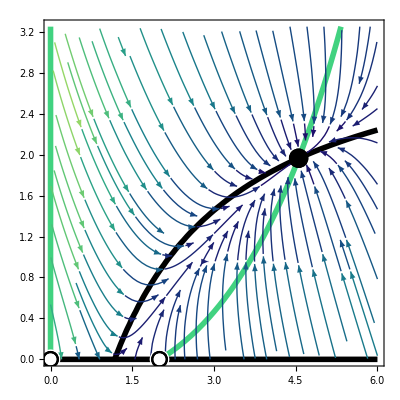

```mathematica
(* Facultative Plants, Obligate Animals *) 
Print["Facultative Plants, Obligate Animals" ]

bP=1; f = 1; g=0.5;γ =0.5;sP=0.05; dP=0.4; 
a=0.85;h=1;
bA=1; ε=1; sA=0.15; dA=1.5;
maxP=6;maxA=3.25;

plantColor =RGBColor[65/256,211/256,129/256];
animalColor = Black;
pointSize = 0.035;
imageSize=15;
lineThickness = 0.01;

(*Non-trivial nullcline equations for model. Using these to plot avoids numerical plotting issues.*)
nP[P_,A_]=bP*f*(g+γ*(a*A)/(1+a*h*P+a*A))-sP*P-dP; 
nA[P_,A_]=bA+ε*(a*P)/(1+a*h*P)-sA*A - dA;
(* Vector Plot *)
(*vp=Evaluate[VectorPlot[{nP[P,A],nA[P,A]},{P,minP,maxP},{A,minA,maxA},Axes->True,AxesLabel->{"P","A"},VectorPoints->8,VectorStyle->{Thick},VectorScale-> {0.08,0.8,None},VectorColorFunction->"BlueGreenYellow"]];*)

(* Stream Plot *) 
sp=Evaluate[StreamPlot[{nP[P,A],nA[P,A]},{P,minP,maxP},{A,minA,maxA},Axes->True,StreamColorFunction->"BlueGreenYellow", StreamScale->Large]];

(* Non-Trivial Nullclines *)
cpP=ContourPlot[{nP[P,A]==0},{P,minP,maxP},{A,minA,maxA}, ColorFunction->Function[{x},plantColor],ContourStyle->{Thickness[lineThickness]}];
cpA=ContourPlot[{nA[P,A]==0},{P,minP,maxP},{A,minA,maxA}, ColorFunction->Function[{x},animalColor],ContourStyle->{Thickness[lineThickness]}];

(* Trivial Nullclines *)
zeroP=Line[{{0,minA},{0,maxA}}]; 
trivialP=Graphics[{Thickness[lineThickness],plantColor,zeroP}];
zeroA=Line[{{minP,0},{maxP,0}}]; 
trivialA=Graphics[{Thickness[lineThickness],animalColor,zeroA}];

(* Asymptotes [Saturation Points] *)
saturA = ε/(h*sA)+(bA-dA)/(sA);
asympA = Line[{{minA,saturA},{maxA,saturA}}];
asympA=Graphics[{Thickness[lineThickness],Dashing[{0.03,0.05,0.03}],animalColor,asympA}];

(* Trivial & Single-Species Equilibria *) 
plantonlyeq = {(bP*f*g-dP)/sP,0} 
preplantonlypt = ListPlot[{plantonlyeq}, PlotStyle->{White, PointSize[pointSize]}];
plantonlypt=ListPlot[{plantonlyeq},PlotMarkers->Graphics[{Black,Circle[]},ImageSize->imageSize]];
 
animalonlyeq={0,(bA-dA)/sA}
preanimalonlypt=ListPlot[{animalonlyeq},PlotStyle->{White, PointSize[pointSize]}];
animalonlypt=ListPlot[{animalonlyeq},PlotMarkers->Graphics[{Black, Circle[]},ImageSize->imageSize]];

trivialeq={0,0};
pretrivialpt=ListPlot[{trivialeq},PlotStyle->{White,PointSize[pointSize]}]; 
trivialpt=ListPlot[{trivialeq},PlotMarkers->Graphics[{Black,Circle[]},ImageSize->imageSize]];

(* Coexistence Equilibria *) 
(*Finds the equilibria for the model. I manually assigned names for unstable and stable equilbiria.*)
equilibria= NSolve[nP[P,A]==0&&nA[P,A]==0&&P>0&&A>0,{P,A}];
equilibria

coexist1={P/.equilibria[[1]],A/.equilibria[[1]]};
precoexistpt1=ListPlot[{coexist1},PlotStyle->{Black, PointSize[0.035]}];
coexistpt1=ListPlot[{coexist1},PlotMarkers->Graphics[{Black,Circle[]},ImageSize->imageSize]];

Show[cpP, cpA,trivialP,trivialA, sp,pretrivialpt,trivialpt, preanimalonlypt,animalonlypt,preplantonlypt,plantonlypt, precoexistpt1, coexistpt1,PlotRangePadding->{{maxP*0.025,0},{maxA*0.025,0}}]
```

Facultative Plants, Facultative Animals

{2.,0}

{0,2.}

{{P→6.56047,A→6.33867}}

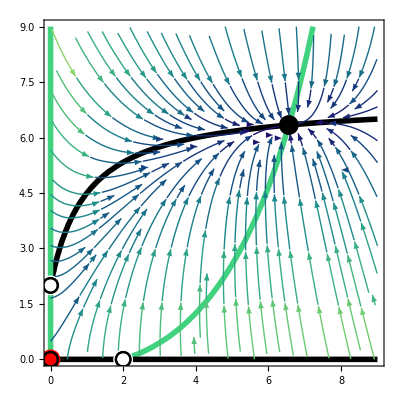

```mathematica
(* Facultative Plants, Facultative Animals *) 
Print["Facultative Plants, Facultative Animals" ]

bP=1; f = 1; g=0.5;γ =0.5;sP=0.05; dP=0.4; 
a=1;h=1;
bA=1; ε=1; sA=0.2; dA=0.6;
maxP=9;maxA=9;

plantColor =RGBColor[65/256,211/256,129/256];
animalColor = Black;
pointSize = 0.035;
imageSize=15;
lineThickness = 0.01;

(*Non-trivial nullcline equations for model. Using these to plot avoids numerical plotting issues.*)
nP[P_,A_]=bP*f*(g+γ*(a*A)/(1+a*h*P+a*A))-sP*P-dP; 
nA[P_,A_]=bA+ε*(a*P)/(1+a*h*P)-sA*A - dA;
(* Vector Plot *)
(*vp=Evaluate[VectorPlot[{nP[P,A],nA[P,A]},{P,minP,maxP},{A,minA,maxA},Axes->True,AxesLabel->{"P","A"},VectorPoints->8,VectorStyle->{Thick},VectorScale-> {0.08,0.8,None},VectorColorFunction->"BlueGreenYellow"]];*)

(* Stream Plot *) 
sp=Evaluate[StreamPlot[{nP[P,A],nA[P,A]},{P,minP,maxP},{A,minA,maxA},Axes->True,StreamColorFunction->"BlueGreenYellow", StreamScale->Large]];

(* Non-Trivial Nullclines *)
cpP=ContourPlot[{nP[P,A]==0},{P,minP,maxP},{A,minA,maxA}, ColorFunction->Function[{x},plantColor],ContourStyle->{Thickness[lineThickness]}];
cpA=ContourPlot[{nA[P,A]==0},{P,minP,maxP},{A,minA,maxA}, ColorFunction->Function[{x},animalColor],ContourStyle->{Thickness[lineThickness]}];

(* Trivial Nullclines *)
zeroP=Line[{{0,minA},{0,maxA}}]; 
trivialP=Graphics[{Thickness[lineThickness],plantColor,zeroP}];
zeroA=Line[{{minP,0},{maxP,0}}]; 
trivialA=Graphics[{Thickness[lineThickness],animalColor,zeroA}];

(* Asymptotes [Saturation Points] *)
saturA = ε/(h*sA)+(bA-dA)/(sA);
asympA = Line[{{minA,saturA},{maxA,saturA}}];
asympA=Graphics[{Thickness[lineThickness],Dashing[{0.03,0.05,0.03}],animalColor,asympA}];

(* Trivial & Single-Species Equilibria *) 
plantonlyeq = {(bP*f*g-dP)/sP,0} 
preplantonlypt = ListPlot[{plantonlyeq}, PlotStyle->{White, PointSize[pointSize]}];
plantonlypt=ListPlot[{plantonlyeq},PlotMarkers->Graphics[{Black,Circle[]},ImageSize->imageSize]];
 
animalonlyeq={0,(bA-dA)/sA}
preanimalonlypt=ListPlot[{animalonlyeq},PlotStyle->{White, PointSize[pointSize]}];
animalonlypt=ListPlot[{animalonlyeq},PlotMarkers->Graphics[{Black, Circle[]},ImageSize->imageSize]];

trivialeq={0,0};
pretrivialpt=ListPlot[{trivialeq},PlotStyle->{Red,PointSize[pointSize]}]; 
trivialpt=ListPlot[{trivialeq},PlotMarkers->Graphics[{Black,Circle[]},ImageSize->imageSize]];

(* Coexistence Equilibria *) 
(*Finds the equilibria for the model. I manually assigned names for unstable and stable equilbiria.*)
equilibria= NSolve[nP[P,A]==0&&nA[P,A]==0&&P>0&&A>0,{P,A}];
equilibria

coexist1={P/.equilibria[[1]],A/.equilibria[[1]]};
precoexistpt1=ListPlot[{coexist1},PlotStyle->{Black, PointSize[0.035]}];
coexistpt1=ListPlot[{coexist1},PlotMarkers->Graphics[{Black,Circle[]},ImageSize->imageSize]];

Show[cpP, cpA,trivialP,trivialA, sp,pretrivialpt,trivialpt, preanimalonlypt,animalonlypt,preplantonlypt,plantonlypt, precoexistpt1, coexistpt1,PlotRangePadding->{{maxP*0.025,0},{maxA*0.025,0}}]
```